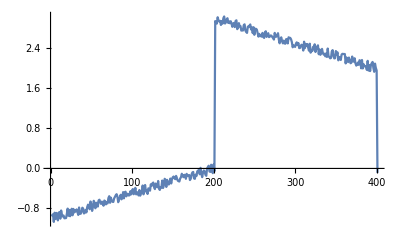

{{1}→0.00411678,{0,1}→0.00198847,{0,0,1}→0.00120159,{0,0,0,1}→0.0200277,{0,0,0,0}→0.972665}

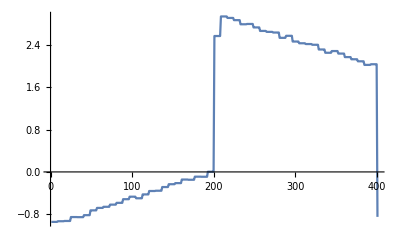

```mathematica
z[x_] = Piecewise[{{x,-1≤x<=0},{3-x,0<x<1}},0];
data=Table[z[x]+RandomReal[{-0.1,0.1}],{x,-1,1,0.005}];
ListLinePlot[data]
dwd=DiscreteWaveletTransform[data,HaarWavelet[],4];
efrac=dwd["EnergyFraction"]
eth[x_,ind_]:=If[(ind/.efrac)<0.01,x*0.,x]/;MemberQ[efrac[[All,1]],ind]
eth[x_,___]:=x
WaveletMapIndexed[eth,dwd];
WaveletMapIndexed[eth,dwd];
ListLinePlot[InverseWaveletTransform[%]]
```

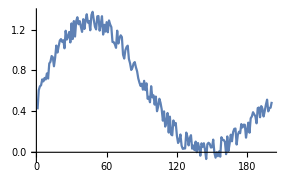

```mathematica
data=Table[0.5+E^-x Sin[2 Pi x]+RandomReal[{-0.1,0.1}],{x,0,1,0.005}];
ListLinePlot[data]
```

{{1}→0.00323369,{0,1}→0.00205146,{0,0,1}→0.0020139,{0,0,0}→0.992701}

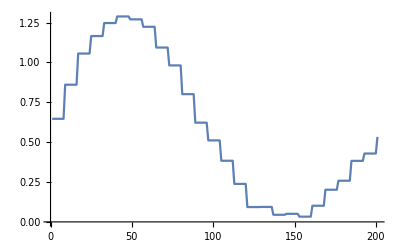

```mathematica
dwd=DiscreteWaveletTransform[data,HaarWavelet[],3];
efrac=dwd["EnergyFraction"]
eth[x_,ind_]:=If[(ind/.efrac)<0.01,x*0.,x]/;MemberQ[efrac[[All,1]],ind]
eth[x_,___]:=x
WaveletMapIndexed[eth,dwd];
WaveletMapIndexed[eth,dwd];
ListLinePlot[InverseWaveletTransform[%]]
```

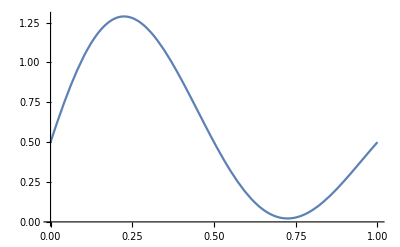

```mathematica
Plot[E^-x Sin[2 Pi x] + 0.5,{x,0,1}]
```